## Bounds on Scalar-Tensor Theory From GW1510914

```mathematica
data1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"] (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184},16330,{-0.960167,432.955,1.12358,4,0.423524,0.156429,0.304489}}
 |  |  |  |

```mathematica
data2=Import[NotebookDirectory[]<>"/-1pn-beta.csv","CSV"]  (*PPE beta*)
data3=Import[NotebookDirectory[]<>"/-1pn-alpha.csv","CSV"] (*PPE alpha*)
```

{{0.0000950433},{0.0000987158},{0.0000994462},{0.0000975037},{0.000095235},{0.000107632},{0.0000997691},16318,{0.0000986108},{0.0000999129},{0.0000988982},{0.0000984216},{0.000105075},{0.000104439},{0.000101563}}
 |  |  |  |

{{0.01842},{0.0193342},{0.0178007},{0.0192073},{0.0183703},{0.0168826},{0.0198715},{0.0176301},16317,{0.0177703},{0.0182836},{0.0180834},{0.0181399},{0.0177094},{0.0174525},{0.0190105}}
 |  |  |  |

```mathematica
Length[data3]
```

16332

```mathematica
χ1=data1[[All,7]]; (*Dimensionles spin parameter*)
χ2=data1[[All,8]];
```

```mathematica
DL=data1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,16318,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,16317,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1=data1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 
(*Ligo posterior gives mass in detector frame. We have to convert it source frame*)
```

{0.000164382,0.000172434,0.000186598,0.000166746,0.000160002,0.000214392,0.000176635,16319,0.000185522,0.000178181,0.000180393,0.000202519,0.000202124,0.000185951}
 |  |  |  |

```mathematica
m2=data1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,16319,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
η=(m1*m2)/(m1+m2)^2;
```

```mathematica
βppE=1.64485*data2[[All,1]](*90% CL upper bound*)
αppE=1.64485*data3[[All,1]](*90% CL upper bound*)
```

{0.000156332,0.000162373,0.000163574,0.000160379,0.000156647,0.000177039,0.000164105,16319,0.000164342,0.000162673,0.000161889,0.000172832,0.000171786,0.000167056}
 |  |  |  |

{0.0302981,0.0318019,0.0292794,0.0315932,0.0302164,0.0277693,0.0326856,0.0289989,16317,0.0292295,0.0300739,0.0297445,0.0298373,0.0291293,0.0287067,0.0312694}
 |  |  |  |

```mathematica
s1=(1+√(1-χ1^2))/2 (*Sensitivity in scalar-tensor*)
s2=(1+√(1-χ2^2))/2
```

{0.959525,0.853652,0.999912,0.996693,0.957429,0.994472,0.998851,0.990716,16316,0.987879,0.908264,0.999229,0.999989,0.99078,0.686606,0.999659,0.996928}
 |  |  |  |

{0.999726,0.950278,0.977818,0.995736,0.971108,0.999458,0.958939,0.958736,16316,0.59088,0.981882,0.999959,0.999904,0.999962,0.914585,0.975786,0.952943}
 |  |  |  |

```mathematica
ϕdotSquared=Abs[-1792/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*βppE]
```

{7.07075×10^9,5.2035×10^9,3.36337×10^7,1.46918×10^11,4.72384×10^9,1.60231×10^7,2.87701×10^8,16318,1.03073×10^8,6.35853×10^7,7.42652×10^7,8.96119×10^7,2.034×10^8,2.10287×10^7,5.7791×10^7}
 |  |  |  |

```mathematica
√Mean[ϕdotSquared]//ScientificForm (*A rough estimat of phidot*)
```

1.12166×10^6

```mathematica
ϕdotSquaredamp=Abs[-48/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*αppE]
```

{3.6706×10^10,2.72985×10^10,1.6126×10^8,7.75217×10^11,2.44072×10^10,6.73205×10^7,1.5349×10^9,16318,4.97528×10^8,3.11674×10^8,3.63731×10^8,4.42397×10^8,9.18246×10^8,9.41264×10^7,2.89747×10^8}
 |  |  |  |

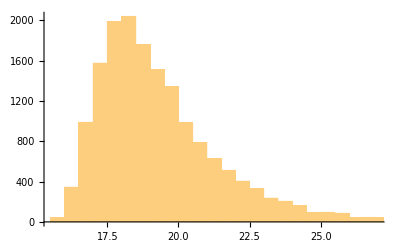

```mathematica
Histogram[Log[ϕdotSquared]]
```

ϕ̇ from phase correction:

```mathematica
LogSquaredϕdotPhase=Log[ϕdotSquared] (*This is Log of sigma_(alpha^2)*)
```

{22.6792,22.3726,17.331,25.7131,22.2759,16.5895,19.4774,17.8745,16316,15.9045,18.4509,17.9679,18.1232,18.311,19.1307,16.8614,17.8723}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotPhase]
```

15.5497

```mathematica
Max[LogSquaredϕdotPhase]
```

36.5124

```mathematica
𝒟logϕHist=HistogramDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕHist2=PDF[𝒟logϕHist,x];
```

```mathematica
𝒟logϕHist3[x_]=𝒟logϕHist2;
```

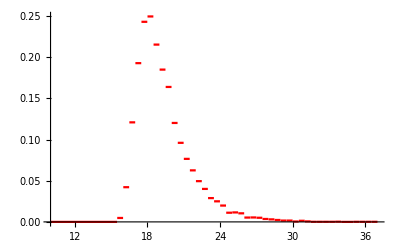

```mathematica
Plot1=Plot[𝒟logϕHist3[x],{x,10,37},PlotStyle->Red]
```

```mathematica
𝒟logϕdotSq=SmoothKernelDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2=PDF[𝒟logϕdotSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], 14.3281≤x≤37.734}, {0, True}}]

```mathematica
𝒟logϕdotSq3[x_]=𝒟logϕdotSq2
```

Piecewise[{{InterpolatingFunction[…][x], 14.3281≤x≤37.734}, {0, True}}]

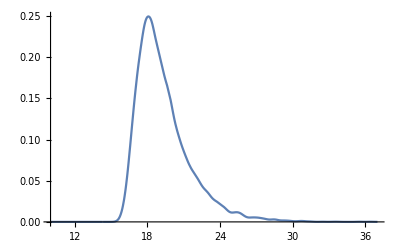

```mathematica
Plot2=Plot[𝒟logϕdotSq3[x],{x,10,37}]
```

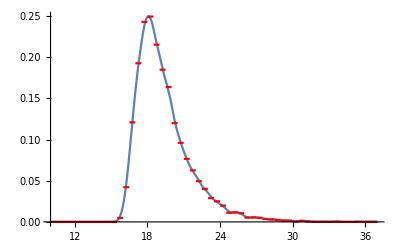

```mathematica
Show[Plot2,Plot1] (*SmoothKernelDistribution is good enough. We do not need to interpolate the acutual histogram*)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
ϕdotSqLogSample=Prepend[10^Range[-1,11,0.1],0]
```

{0,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11}

```mathematica
fun1ϕdotphaseTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ϕdotSqLogFinalPDFPhase=Table[{fun1ϕdotphaseTable[y][[i,1]],NIntegrate[fun1ϕdotphaseTable[y][[i,2]]*𝒟logϕdotSq3[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotphaseTable[y]]}]
```

{{0,5.67008×10^-9},{0.1,5.67008×10^-9},{0.125893,5.67008×10^-9},{0.158489,5.67008×10^-9},{0.199526,5.67008×10^-9},{0.251189,5.67008×10^-9},{0.316228,5.67008×10^-9},{0.398107,5.67008×10^-9},{0.501187,5.67008×10^-9},{0.630957,5.67008×10^-9},{0.794328,5.67008×10^-9},{1.,5.67008×10^-9},{1.25893,5.67008×10^-9},{1.58489,5.67008×10^-9},{1.99526,5.67008×10^-9},{2.51189,5.67008×10^-9},{3.16228,5.67008×10^-9},{3.98107,5.67008×10^-9},{5.01187,5.67008×10^-9},{6.30957,5.67008×10^-9},{7.94328,5.67008×10^-9},{10.,5.67008×10^-9},{12.5893,5.67008×10^-9},{15.8489,5.67008×10^-9},{19.9526,5.67008×10^-9},{25.1189,5.67008×10^-9},{31.6228,5.67008×10^-9},{39.8107,5.67008×10^-9},{50.1187,5.67008×10^-9},{63.0957,5.67008×10^-9},{79.4328,5.67008×10^-9},{100.,5.67008×10^-9},{125.893,5.67008×10^-9},{158.489,5.67008×10^-9},{199.526,5.67008×10^-9},{251.189,5.67008×10^-9},{316.228,5.67008×10^-9},{398.107,5.67008×10^-9},{501.187,5.67008×10^-9},{630.957,5.67008×10^-9},{794.328,5.67008×10^-9},{1000.,5.67008×10^-9},{1258.93,5.67008×10^-9},{1584.89,5.67008×10^-9},{1995.26,5.67008×10^-9},{2511.89,5.67008×10^-9},{3162.28,5.67008×10^-9},{3981.07,5.67008×10^-9},{5011.87,5.67008×10^-9},{6309.57,5.67008×10^-9},{7943.28,5.67008×10^-9},{10000.,5.67007×10^-9},{12589.3,5.67007×10^-9},{15848.9,5.67007×10^-9},{19952.6,5.67007×10^-9},{25118.9,5.67007×10^-9},{31622.8,5.67007×10^-9},{39810.7,5.67006×10^-9},{50118.7,5.67005×10^-9},{63095.7,5.67004×10^-9},{79432.8,5.67002×10^-9},{100000.,5.66999×10^-9},{125893.,5.66994×10^-9},{158489.,5.66987×10^-9},{199526.,5.66974×10^-9},{251189.,5.66955×10^-9},{316228.,5.66924×10^-9},{398107.,5.66875×10^-9},{501187.,5.66798×10^-9},{630957.,5.66676×10^-9},{794328.,5.66482×10^-9},{1.×10^6,5.66175×10^-9},{1.25893×10^6,5.6569×10^-9},{1.58489×10^6,5.64925×10^-9},{1.99526×10^6,5.63722×10^-9},{2.51189×10^6,5.61834×10^-9},{3.16228×10^6,5.58893×10^-9},{3.98107×10^6,5.54352×10^-9},{5.01187×10^6,5.47437×10^-9},{6.30957×10^6,5.37114×10^-9},{7.94328×10^6,5.22126×10^-9},{1.×10^7,5.01152×10^-9},{1.25893×10^7,4.73132×10^-9},{1.58489×10^7,4.37696×10^-9},{1.99526×10^7,3.95529×10^-9},{2.51189×10^7,3.4844×10^-9},{3.16228×10^7,2.99048×10^-9},{3.98107×10^7,2.50191×10^-9},{5.01187×10^7,2.04323×10^-9},{6.30957×10^7,1.63155×10^-9},{7.94328×10^7,1.27596×10^-9},{1.×10^8,9.79044×10^-10},{1.25893×10^8,7.38817×10^-10},{1.58489×10^8,5.50056×10^-10},{1.99526×10^8,4.05407×10^-10},{2.51189×10^8,2.96616×10^-10},{3.16228×10^8,2.15769×10^-10},{3.98107×10^8,1.56119×10^-10},{5.01187×10^8,1.12361×10^-10},{6.30957×10^8,8.04697×10^-11},{7.94328×10^8,5.74122×10^-11},{1.×10^9,4.08929×10^-11},{1.25893×10^9,2.91462×10^-11},{1.58489×10^9,2.08136×10^-11},{1.99526×10^9,1.48889×10^-11},{2.51189×10^9,1.06617×10^-11},{3.16228×10^9,7.63759×10^-12},{3.98107×10^9,5.46944×10^-12},{5.01187×10^9,3.91172×10^-12},{6.30957×10^9,2.79143×10^-12},{7.94328×10^9,1.9869×10^-12},{1.×10^10,1.41127×10^-12},{1.25893×10^10,1.00087×10^-12},{1.58489×10^10,7.08778×10^-13},{1.99526×10^10,5.01144×10^-13},{2.51189×10^10,3.53862×10^-13},{3.16228×10^10,2.4957×10^-13},{3.98107×10^10,1.75759×10^-13},{5.01187×10^10,1.23677×10^-13},{6.30957×10^10,8.72261×10^-14},{7.94328×10^10,6.19301×10^-14},{1.×10^11,4.43497×10^-14}}

```mathematica
ϕdotSqLogFinalPDFPhaseInterp=Interpolation[ϕdotSqLogFinalPDFPhase]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalization=NIntegrate[ϕdotSqLogFinalPDFPhaseInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.490203

```mathematica
ϕdotSqLogFinalPDFPhaseNorm=Table[{ϕdotSqLogFinalPDFPhase[[i,1]],ϕdotSqLogFinalPDFPhase[[i,2]]/ϕdotSqNormalization},{i,1,Length[ϕdotSqLogFinalPDFPhase]}];
```

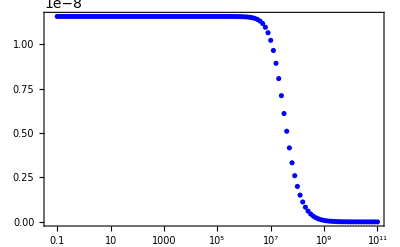

```mathematica
plotϕdotSqFinalPDFPhaseLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFPhaseNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFPhaseInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFPhaseNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFPhaseInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

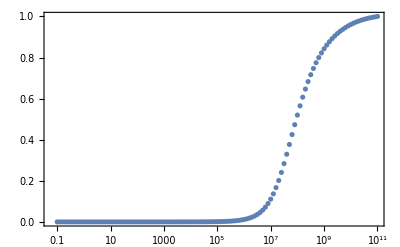

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFPhaseNormInterp=Interpolation[ϕdotSqFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLphase=x/.FindRoot[ϕdotSqFinalCDFPhaseNormInterp[x]==0.9,{x,10^8}]
```

2.29378×10^9

```mathematica
√ϕdotSq90CLphase//ScientificForm (*90% CL upper bound on scalar-tensor from phase*)
```

4.78934×10^4

```mathematica
ϕ̇ from amplitude correction:
```

```mathematica
LogSquaredϕdotamp=Log[ϕdotSquaredamp]
```

{24.3262,24.0301,18.8985,27.3764,23.9181,18.025,21.1517,19.4518,16316,17.4767,20.0252,19.5575,19.7119,19.9077,20.638,18.3601,19.4845}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotamp]
```

16.9279

```mathematica
Max[LogSquaredϕdotamp]
```

38.1608

```mathematica
Histogram[LogSquaredϕdotamp];
```

```mathematica
𝒟logϕdotSqamp=SmoothKernelDistribution[LogSquaredϕdotamp]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSqamp2=PDF[𝒟logϕdotSqamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 15.6812≤x≤39.4075}, {0, True}}]

```mathematica
𝒟logϕdotSqamp3[x_]=𝒟logϕdotSqamp2
```

Piecewise[{{InterpolatingFunction[…][x], 15.6812≤x≤39.4075}, {0, True}}]

```mathematica
Plot2=Plot[𝒟logϕdotSqamp3[x],{x,7,40},PlotRange->All];
```

```mathematica
ϕdotSqLogSampleamp=Prepend[10^Range[-1,11,0.1],0];
```

```mathematica
fun1ϕdotampTable[y_]=Table[{ϕdotSqLogSampleamp[[i]],fun1αphase[ϕdotSqLogSampleamp[[i]],y]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

```mathematica
ϕdotSqLogFinalPDFamp=Table[{fun1ϕdotampTable[y][[i,1]],NIntegrate[fun1ϕdotampTable[y][[i,2]]*𝒟logϕdotSqamp3[y],{y,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]},{i,1,Length[fun1ϕdotampTable[y]]}]
```

{{0,1.18344×10^-9},{0.1,1.18344×10^-9},{0.125893,1.18344×10^-9},{0.158489,1.18344×10^-9},{0.199526,1.18344×10^-9},{0.251189,1.18344×10^-9},{0.316228,1.18344×10^-9},{0.398107,1.18344×10^-9},{0.501187,1.18344×10^-9},{0.630957,1.18344×10^-9},{0.794328,1.18344×10^-9},{1.,1.18344×10^-9},{1.25893,1.18344×10^-9},{1.58489,1.18344×10^-9},{1.99526,1.18344×10^-9},{2.51189,1.18344×10^-9},{3.16228,1.18344×10^-9},{3.98107,1.18344×10^-9},{5.01187,1.18344×10^-9},{6.30957,1.18344×10^-9},{7.94328,1.18344×10^-9},{10.,1.18344×10^-9},{12.5893,1.18344×10^-9},{15.8489,1.18344×10^-9},{19.9526,1.18344×10^-9},{25.1189,1.18344×10^-9},{31.6228,1.18344×10^-9},{39.8107,1.18344×10^-9},{50.1187,1.18344×10^-9},{63.0957,1.18344×10^-9},{79.4328,1.18344×10^-9},{100.,1.18344×10^-9},{125.893,1.18344×10^-9},{158.489,1.18344×10^-9},{199.526,1.18344×10^-9},{251.189,1.18344×10^-9},{316.228,1.18344×10^-9},{398.107,1.18344×10^-9},{501.187,1.18344×10^-9},{630.957,1.18344×10^-9},{794.328,1.18344×10^-9},{1000.,1.18344×10^-9},{1258.93,1.18344×10^-9},{1584.89,1.18344×10^-9},{1995.26,1.18344×10^-9},{2511.89,1.18344×10^-9},{3162.28,1.18344×10^-9},{3981.07,1.18344×10^-9},{5011.87,1.18344×10^-9},{6309.57,1.18344×10^-9},{7943.28,1.18344×10^-9},{10000.,1.18344×10^-9},{12589.3,1.18344×10^-9},{15848.9,1.18344×10^-9},{19952.6,1.18344×10^-9},{25118.9,1.18344×10^-9},{31622.8,1.18344×10^-9},{39810.7,1.18344×10^-9},{50118.7,1.18344×10^-9},{63095.7,1.18344×10^-9},{79432.8,1.18344×10^-9},{100000.,1.18344×10^-9},{125893.,1.18344×10^-9},{158489.,1.18344×10^-9},{199526.,1.18344×10^-9},{251189.,1.18343×10^-9},{316228.,1.18343×10^-9},{398107.,1.18342×10^-9},{501187.,1.18342×10^-9},{630957.,1.1834×10^-9},{794328.,1.18338×10^-9},{1.×10^6,1.18335×10^-9},{1.25893×10^6,1.18329×10^-9},{1.58489×10^6,1.18321×10^-9},{1.99526×10^6,1.18308×10^-9},{2.51189×10^6,1.18286×10^-9},{3.16228×10^6,1.18253×10^-9},{3.98107×10^6,1.18199×10^-9},{5.01187×10^6,1.18115×10^-9},{6.30957×10^6,1.17982×10^-9},{7.94328×10^6,1.17773×10^-9},{1.×10^7,1.17445×10^-9},{1.25893×10^7,1.16932×10^-9},{1.58489×10^7,1.1614×10^-9},{1.99526×10^7,1.14929×10^-9},{2.51189×10^7,1.13114×10^-9},{3.16228×10^7,1.1046×10^-9},{3.98107×10^7,1.06708×10^-9},{5.01187×10^7,1.01624×10^-9},{6.30957×10^7,9.50757×10^-10},{7.94328×10^7,8.71096×10^-10},{1.×10^8,7.799×10^-10},{1.25893×10^8,6.81677×10^-10},{1.58489×10^8,5.81814×10^-10},{1.99526×10^8,4.85377×10^-10},{2.51189×10^8,3.96257×10^-10},{3.16228×10^8,3.16911×10^-10},{3.98107×10^8,2.48554×10^-10},{5.01187×10^8,1.91455×10^-10},{6.30957×10^8,1.45163×10^-10},{7.94328×10^8,1.08663×10^-10},{1.×10^9,8.05516×10^-11},{1.25893×10^9,5.92674×10^-11},{1.58489×10^9,4.33278×10^-11},{1.99526×10^9,3.14764×10^-11},{2.51189×10^9,2.27239×10^-11},{3.16228×10^9,1.6311×10^-11},{3.98107×10^9,1.1655×10^-11},{5.01187×10^9,8.30814×10^-12},{6.30957×10^9,5.92317×10^-12},{7.94328×10^9,4.23023×10^-12},{1.×10^10,3.02674×10^-12},{1.25893×10^10,2.16808×10^-12},{1.58489×10^10,1.55359×10^-12},{1.99526×10^10,1.11287×10^-12},{2.51189×10^10,7.96162×10^-13},{3.16228×10^10,5.68324×10^-13},{3.98107×10^10,4.04606×10^-13},{5.01187×10^10,2.874×10^-13},{6.30957×10^10,2.03836×10^-13},{7.94328×10^10,1.44387×10^-13},{1.×10^11,1.0213×10^-13}}

```mathematica
ϕdotSqLogFinalPDFampInterp=Interpolation[ϕdotSqLogFinalPDFamp]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationamp=NIntegrate[ϕdotSqLogFinalPDFampInterp[x],{x,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]
```

0.47884

```mathematica
ϕdotSqLogFinalPDFampNorm=Table[{ϕdotSqLogFinalPDFamp[[i,1]],ϕdotSqLogFinalPDFamp[[i,2]]/ϕdotSqNormalizationamp},{i,1,Length[ϕdotSqLogFinalPDFamp]}]
```

{{0,2.47147×10^-9},{0.1,2.47147×10^-9},{0.125893,2.47147×10^-9},{0.158489,2.47147×10^-9},{0.199526,2.47147×10^-9},{0.251189,2.47147×10^-9},{0.316228,2.47147×10^-9},{0.398107,2.47147×10^-9},{0.501187,2.47147×10^-9},{0.630957,2.47147×10^-9},{0.794328,2.47147×10^-9},{1.,2.47147×10^-9},{1.25893,2.47147×10^-9},{1.58489,2.47147×10^-9},{1.99526,2.47147×10^-9},{2.51189,2.47147×10^-9},{3.16228,2.47147×10^-9},{3.98107,2.47147×10^-9},{5.01187,2.47147×10^-9},{6.30957,2.47147×10^-9},{7.94328,2.47147×10^-9},{10.,2.47147×10^-9},{12.5893,2.47147×10^-9},{15.8489,2.47147×10^-9},{19.9526,2.47147×10^-9},{25.1189,2.47147×10^-9},{31.6228,2.47147×10^-9},{39.8107,2.47147×10^-9},{50.1187,2.47147×10^-9},{63.0957,2.47147×10^-9},{79.4328,2.47147×10^-9},{100.,2.47147×10^-9},{125.893,2.47147×10^-9},{158.489,2.47147×10^-9},{199.526,2.47147×10^-9},{251.189,2.47147×10^-9},{316.228,2.47147×10^-9},{398.107,2.47147×10^-9},{501.187,2.47147×10^-9},{630.957,2.47147×10^-9},{794.328,2.47147×10^-9},{1000.,2.47147×10^-9},{1258.93,2.47147×10^-9},{1584.89,2.47147×10^-9},{1995.26,2.47147×10^-9},{2511.89,2.47147×10^-9},{3162.28,2.47147×10^-9},{3981.07,2.47147×10^-9},{5011.87,2.47147×10^-9},{6309.57,2.47147×10^-9},{7943.28,2.47147×10^-9},{10000.,2.47147×10^-9},{12589.3,2.47147×10^-9},{15848.9,2.47147×10^-9},{19952.6,2.47147×10^-9},{25118.9,2.47147×10^-9},{31622.8,2.47147×10^-9},{39810.7,2.47147×10^-9},{50118.7,2.47147×10^-9},{63095.7,2.47147×10^-9},{79432.8,2.47147×10^-9},{100000.,2.47147×10^-9},{125893.,2.47147×10^-9},{158489.,2.47147×10^-9},{199526.,2.47146×10^-9},{251189.,2.47146×10^-9},{316228.,2.47145×10^-9},{398107.,2.47144×10^-9},{501187.,2.47142×10^-9},{630957.,2.4714×10^-9},{794328.,2.47135×10^-9},{1.×10^6,2.47128×10^-9},{1.25893×10^6,2.47117×10^-9},{1.58489×10^6,2.47099×10^-9},{1.99526×10^6,2.47071×10^-9},{2.51189×10^6,2.47027×10^-9},{3.16228×10^6,2.46956×10^-9},{3.98107×10^6,2.46845×10^-9},{5.01187×10^6,2.46669×10^-9},{6.30957×10^6,2.46392×10^-9},{7.94328×10^6,2.45955×10^-9},{1.×10^7,2.45269×10^-9},{1.25893×10^7,2.44199×10^-9},{1.58489×10^7,2.42544×10^-9},{1.99526×10^7,2.40016×10^-9},{2.51189×10^7,2.36225×10^-9},{3.16228×10^7,2.30682×10^-9},{3.98107×10^7,2.22846×10^-9},{5.01187×10^7,2.12229×10^-9},{6.30957×10^7,1.98554×10^-9},{7.94328×10^7,1.81918×10^-9},{1.×10^8,1.62873×10^-9},{1.25893×10^8,1.4236×10^-9},{1.58489×10^8,1.21505×10^-9},{1.99526×10^8,1.01365×10^-9},{2.51189×10^8,8.27535×10^-10},{3.16228×10^8,6.61831×10^-10},{3.98107×10^8,5.19076×10^-10},{5.01187×10^8,3.99831×10^-10},{6.30957×10^8,3.03155×10^-10},{7.94328×10^8,2.2693×10^-10},{1.×10^9,1.68222×10^-10},{1.25893×10^9,1.23773×10^-10},{1.58489×10^9,9.04849×10^-11},{1.99526×10^9,6.57347×10^-11},{2.51189×10^9,4.74562×10^-11},{3.16228×10^9,3.40635×10^-11},{3.98107×10^9,2.434×10^-11},{5.01187×10^9,1.73506×10^-11},{6.30957×10^9,1.23698×10^-11},{7.94328×10^9,8.83434×10^-12},{1.×10^10,6.32099×10^-12},{1.25893×10^10,4.52778×10^-12},{1.58489×10^10,3.24449×10^-12},{1.99526×10^10,2.32409×10^-12},{2.51189×10^10,1.66269×10^-12},{3.16228×10^10,1.18688×10^-12},{3.98107×10^10,8.44972×10^-13},{5.01187×10^10,6.00201×10^-13},{6.30957×10^10,4.25687×10^-13},{7.94328×10^10,3.01534×10^-13},{1.×10^11,2.13286×10^-13}}

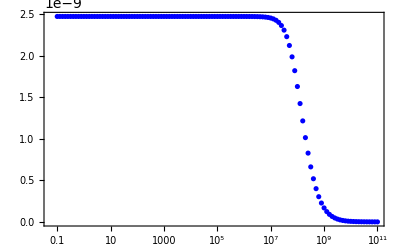

```mathematica
plotϕdotSqFinalPDFampLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFampNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFampInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFampNorm=Table[{ϕdotSqLogSampleamp[[i]],NIntegrate[ϕdotSqFinalPDFampInterpLogNorm[x],{x,Min[ϕdotSqLogSampleamp],ϕdotSqLogSampleamp[[i]]}]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

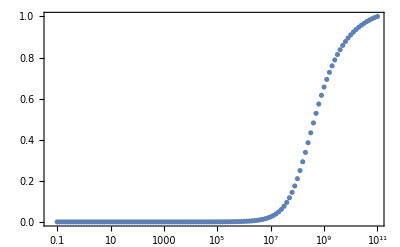

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFampNormInterp=Interpolation[ϕdotSqFinalCDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLamp=x/.FindRoot[ϕdotSqFinalCDFampNormInterp[x]==0.9,{x,10^9}]
```

8.54415×10^9

```mathematica
√ϕdotSq90CLamp//ScientificForm (*90% CL upper boun on \[Phi dot from amp*)
```

9.24346×10^4

```mathematica
Combining the upper bounds of Subscript[α^2, EDGB] from phase and amplitude corrections:
```

```mathematica
ϕdotSquaredcomb=(1/ϕdotSquaredamp^2+1/ϕdotSquared^2)^(-1/2)
```

{6.9431×10^9,5.11147×10^9,3.29252×10^7,1.44348×10^11,4.63777×10^9,1.55877×10^7,2.82776×10^8,16318,1.0093×10^8,6.23019×10^7,7.2764×10^7,8.78282×10^7,1.98586×10^8,2.05228×10^7,5.66747×10^7}
 |  |  |  |

```mathematica
LogϕdotSquaredcomb=Log[ϕdotSquaredcomb] (*This is Log of sigma_(alpha^2)*)
```

{22.661,22.3548,17.3097,25.6955,22.2575,16.562,19.4602,17.8536,16316,15.8834,18.4299,17.9475,18.1027,18.2909,19.1067,16.837,17.8528}
 |  |  |  |

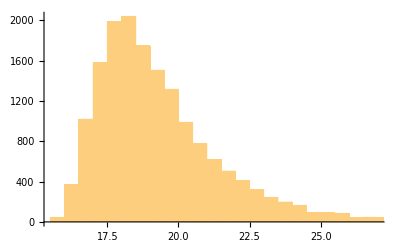

```mathematica
Histogram[LogϕdotSquaredcomb]
```

```mathematica
Min[LogϕdotSquaredcomb]
```

15.5189

```mathematica
Max[LogϕdotSquaredcomb]
```

36.4942

```mathematica
𝒟logϕdotSqcomb=SmoothKernelDistribution[LogϕdotSquaredcomb]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2comb=PDF[𝒟logϕdotSqcomb,x]
```

Piecewise[{{InterpolatingFunction[…][x], 14.2962≤x≤37.7169}, {0, True}}]

```mathematica
𝒟logϕdotSq3comb[x_]=𝒟logϕdotSq2comb
```

Piecewise[{{InterpolatingFunction[…][x], 14.2962≤x≤37.7169}, {0, True}}]

```mathematica
fun1ϕdotcombTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];(*I am using the same sample as the phase*)
```

```mathematica
ϕdotSqLogFinalPDFcomb=Table[{fun1ϕdotcombTable[y][[i,1]],NIntegrate[fun1ϕdotcombTable[y][[i,2]]*𝒟logϕdotSq3comb[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotcombTable[y]]}]
```

{{0,5.79281×10^-9},{0.1,5.79281×10^-9},{0.125893,5.79281×10^-9},{0.158489,5.79281×10^-9},{0.199526,5.79281×10^-9},{0.251189,5.79281×10^-9},{0.316228,5.79281×10^-9},{0.398107,5.79281×10^-9},{0.501187,5.79281×10^-9},{0.630957,5.79281×10^-9},{0.794328,5.79281×10^-9},{1.,5.79281×10^-9},{1.25893,5.79281×10^-9},{1.58489,5.79281×10^-9},{1.99526,5.79281×10^-9},{2.51189,5.79281×10^-9},{3.16228,5.79281×10^-9},{3.98107,5.79281×10^-9},{5.01187,5.79281×10^-9},{6.30957,5.79281×10^-9},{7.94328,5.79281×10^-9},{10.,5.79281×10^-9},{12.5893,5.79281×10^-9},{15.8489,5.79281×10^-9},{19.9526,5.79281×10^-9},{25.1189,5.79281×10^-9},{31.6228,5.79281×10^-9},{39.8107,5.79281×10^-9},{50.1187,5.79281×10^-9},{63.0957,5.79281×10^-9},{79.4328,5.79281×10^-9},{100.,5.79281×10^-9},{125.893,5.79281×10^-9},{158.489,5.79281×10^-9},{199.526,5.79281×10^-9},{251.189,5.79281×10^-9},{316.228,5.79281×10^-9},{398.107,5.79281×10^-9},{501.187,5.79281×10^-9},{630.957,5.79281×10^-9},{794.328,5.79281×10^-9},{1000.,5.79281×10^-9},{1258.93,5.79281×10^-9},{1584.89,5.79281×10^-9},{1995.26,5.79281×10^-9},{2511.89,5.79281×10^-9},{3162.28,5.79281×10^-9},{3981.07,5.79281×10^-9},{5011.87,5.79281×10^-9},{6309.57,5.79281×10^-9},{7943.28,5.79281×10^-9},{10000.,5.79281×10^-9},{12589.3,5.79281×10^-9},{15848.9,5.79281×10^-9},{19952.6,5.79281×10^-9},{25118.9,5.79281×10^-9},{31622.8,5.7928×10^-9},{39810.7,5.7928×10^-9},{50118.7,5.79279×10^-9},{63095.7,5.79278×10^-9},{79432.8,5.79276×10^-9},{100000.,5.79272×10^-9},{125893.,5.79267×10^-9},{158489.,5.79259×10^-9},{199526.,5.79246×10^-9},{251189.,5.79225×10^-9},{316228.,5.79192×10^-9},{398107.,5.79139×10^-9},{501187.,5.79056×10^-9},{630957.,5.78925×10^-9},{794328.,5.78716×10^-9},{1.×10^6,5.78387×10^-9},{1.25893×10^6,5.77866×10^-9},{1.58489×10^6,5.77045×10^-9},{1.99526×10^6,5.75753×10^-9},{2.51189×10^6,5.73729×10^-9},{3.16228×10^6,5.70577×10^-9},{3.98107×10^6,5.65717×10^-9},{5.01187×10^6,5.58331×10^-9},{6.30957×10^6,5.47335×10^-9},{7.94328×10^6,5.31431×10^-9},{1.×10^7,5.09284×10^-9},{1.25893×10^7,4.79869×10^-9},{1.58489×10^7,4.42914×10^-9},{1.99526×10^7,3.99245×10^-9},{2.51189×10^7,3.50817×10^-9},{3.16228×10^7,3.00353×10^-9},{3.98107×10^7,2.50722×10^-9},{5.01187×10^7,2.04352×10^-9},{6.30957×10^7,1.62893×10^-9},{7.94328×10^7,1.27192×10^-9},{1.×10^8,9.74629×10^-10},{1.25893×10^8,7.3469×10^-10},{1.58489×10^8,5.46563×10^-10},{1.99526×10^8,4.02636×10^-10},{2.51189×10^8,2.94495×10^-10},{3.16228×10^8,2.14167×10^-10},{3.98107×10^8,1.54912×10^-10},{5.01187×10^8,1.11456×10^-10},{6.30957×10^8,7.97973×10^-11},{7.94328×10^8,5.69221×10^-11},{1.×10^9,4.05437×10^-11},{1.25893×10^9,2.89015×10^-11},{1.58489×10^9,2.06423×10^-11},{1.99526×10^9,1.47682×10^-11},{2.51189×10^9,1.0576×10^-11},{3.16228×10^9,7.57632×10^-12},{3.98107×10^9,5.42524×10^-12},{5.01187×10^9,3.87954×10^-12},{6.30957×10^9,2.7679×10^-12},{7.94328×10^9,1.96976×10^-12},{1.×10^10,1.39888×10^-12},{1.25893×10^10,9.91966×10^-13},{1.58489×10^10,7.02394×10^-13},{1.99526×10^10,4.96578×10^-13},{2.51189×10^10,3.50609×10^-13},{3.16228×10^10,2.47252×10^-13},{3.98107×10^10,1.74108×10^-13},{5.01187×10^10,1.22521×10^-13},{6.30957×10^10,8.64447×10^-14},{7.94328×10^10,6.14171×10^-14},{1.×10^11,4.40089×10^-14}}

```mathematica
ϕdotSqLogFinalPDFcombInterp=Interpolation[ϕdotSqLogFinalPDFcomb]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationcomb=NIntegrate[ϕdotSqLogFinalPDFcombInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.490281

```mathematica
ϕdotSqLogFinalPDFcombNorm=Table[{ϕdotSqLogFinalPDFcomb[[i,1]],ϕdotSqLogFinalPDFcomb[[i,2]]/ϕdotSqNormalizationcomb},{i,1,Length[ϕdotSqLogFinalPDFcomb]}];
```

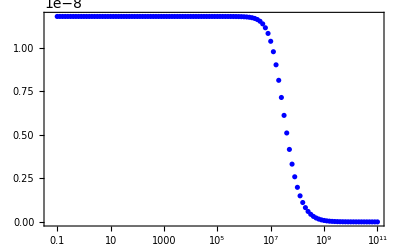

```mathematica
plotϕdotSqFinalPDFcombLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFcombNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFcombInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFcombNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFcombInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True];
```

```mathematica
ϕdotSqFinalCDFcombNormInterp=Interpolation[ϕdotSqFinalCDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLcomb=x/.FindRoot[ϕdotSqFinalCDFcombNormInterp[x]==0.9,{x,10^8}]
```

2.2587×10^9

```mathematica
√ϕdotSq90CLcomb//ScientificForm (*90% CL upper bound on scalar-tensor from combined pdf*)
```

4.75258×10^4

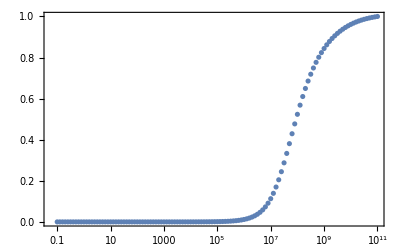

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True]
```

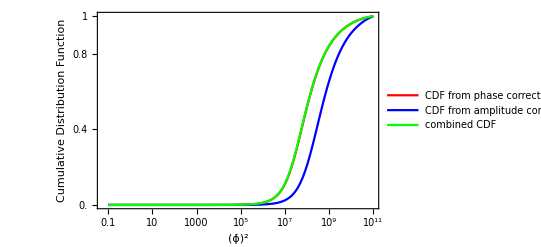

```mathematica
PlotCDFComparisonAll=ListLogLinearPlot[{ϕdotSqFinalCDFPhaseNorm,ϕdotSqFinalCDFampNorm,ϕdotSqFinalCDFcombNorm},Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Green},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction","combined CDF"},LabelStyle->{Orange,FontSize->5},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Bottom}]},FrameLabel->{"(ϕ̇)^2","Cumulative Distribution Function"},FrameStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{Automatic,{0.0,0.2,0.4,0.6,0.8,0.9,1}},FrameTicksStyle->Directive[Black,9]]
```

## Small Coupling Approximation:

```mathematica
𝒟logphase=HistogramDistribution[Log[m1*√ϕdotSquared]]
```

DataDistribution[…]

```mathematica
Max[Log[m1*√ϕdotSquared]]
```

9.56039

```mathematica
ps1=PDF[𝒟logphase,x];
ps2[x]=ps1;
```

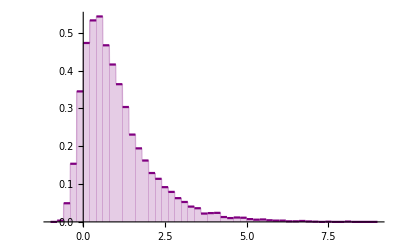

```mathematica
Plot[ps2[x],{x,-1,9},Filling->Axis,PlotStyle->Purple,PlotRange->All]
```

```mathematica
Integrate[ps2[x],{x,Log[Min[m1*√ϕdotSquared]],Log[Max[m1*√ϕdotSquared]]}]
```

0.999633

```mathematica
Integrate[ps2[x],{x,Log[Min[m1*√ϕdotSquared]],0}]*100 (*11% satisfies small coupling approximation*)
```

10.9931

```mathematica
𝒟logphase=HistogramDistribution[Log[m1*√ϕdotSquared]]
```

DataDistribution[…]

```mathematica
𝒟logamp=HistogramDistribution[Log[m1*√ϕdotSquaredamp]]
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[m1*√ϕdotSquaredamp]]
```

0.04206

```mathematica
Max[Log[m1*√ϕdotSquaredamp]]
```

10.3846

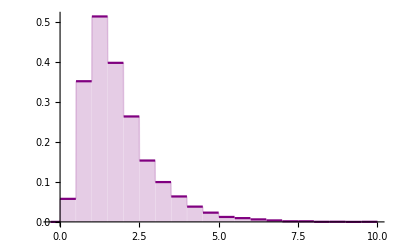

```mathematica
Plot[ps2amp[x],{x,-0.3,10},Filling->Axis,PlotStyle->Purple,PlotRange->All]
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√ϕdotSquaredamp]],Log[Max[m1*√ϕdotSquaredamp]]}]
```

0.997546

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√ϕdotSquaredamp]],0}]*100 (*0.2% satisfies small coupling approximation*)
```

-0.242594

Check for other events:

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->1.46,m2t->1.27,s1t->1,s2t->1,ηt->(1.46*1.27/(1.46+1.27)^2)} (*GW170608*)
```

1.9214

```mathematica
((10^-4*1792/5 ηt^(-2/5))/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->50.6,m2t->34.3,s1t->1,s2t->1,ηt->(50.6*34.3/(50.6+34.3)^2)} (*GW170729*)
```

0.781306

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.6,m2t->30.6,s1t->1,s2t->1,ηt->(35.6*30./(35.6+30.6)^2)}  (*GW150914*)
```

1.78769

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->13.7,m2t->7.7,s1t->1,s2t->1,ηt->(13.7*7.7/(13.7+7.7)^2)}  (*GW151226*)
```

0.579798

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->23.3,m2t->13.6,s1t->1,s2t->1,ηt->(23.3*13.6/(23.3+13.6)^2)}  (*GW151012*)
```

0.608695

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->39.6,m2t->29.4,s1t->1,s2t->1,ηt->(39.6*29.4/(39.6+29.4)^2)}  (*GW170823*)
```

0.974115

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.5,m2t->26.4,s1t->1,s2t->1,ηt->(35.5*26.8/(35.5+26.8)^2)}  (*GW170818*)
```

0.978348

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->30.7,m2t->25.3,s1t->1,s2t->1,ηt->(30.7*25.3/(30.7+25.3)^2)}  (*GW170814*)
```

1.42283

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.2,m2t->23.8,s1t->1,s2t->1,ηt->(35.2*25.8/(35.2+25.8)^2)}  (*GW170809*)
```

0.775035

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->31.,m2t->20.1,s1t->1,s2t->1,ηt->(31*20.1/(31+20.1)^2)}  (*GW170104*)
```

0.717094